# Formal checks of GENETICS manuscript 302005 by Sakamoto and Innan

## Obtaining Equation 3

From Equation 2 in the manuscript:

```mathematica
u[x1_,x2_]:=1-Exp[-2N1 x1 ψ1-2N2 x2 ψ2]
```

```mathematica
eq1LHS:=x1/(4N1)D[u[x1,x2],{x1,2}]+x2/(4N2)D[u[x1,x2],{x2,2}]+(s1 x1+m1(x2-x1))D[u[x1,x2],x1]+(s2 x2+m2(x1-x2))D[u[x1,x2],x2]
```

```mathematica
eq1:=eq1LHS==0
```

```mathematica
eq1
```

2 ⅇ^(-2 N1 x1 ψ1-2 N2 x2 ψ2) N1 (s1 x1+m1 (-x1+x2)) ψ1-ⅇ^(-2 N1 x1 ψ1-2 N2 x2 ψ2) N1 x1 ψ1^2+2 ⅇ^(-2 N1 x1 ψ1-2 N2 x2 ψ2) N2 (m2 (x1-x2)+s2 x2) ψ2-ⅇ^(-2 N1 x1 ψ1-2 N2 x2 ψ2) N2 x2 ψ2^2==0

```mathematica
term1=Factor[eq1LHS]
```

-ⅇ^(-2 N1 x1 ψ1-2 N2 x2 ψ2) (2 m1 N1 x1 ψ1-2 N1 s1 x1 ψ1-2 m1 N1 x2 ψ1+N1 x1 ψ1^2-2 m2 N2 x1 ψ2+2 m2 N2 x2 ψ2-2 N2 s2 x2 ψ2+N2 x2 ψ2^2)

Equation ‘eq1’ has (a) solution(s) if the term in brackets in the expression ‘term1’ above is zero. The term in brackets cannot be further factorised.

```mathematica
term2=Factor[2 m1 N1 x1 ψ1-2 N1 s1 x1 ψ1-2 m1 N1 x2 ψ1+N1 x1 ψ1^2-2 m2 N2 x1 ψ2+2 m2 N2 x2 ψ2-2 N2 s2 x2 ψ2+N2 x2 ψ2^2]
```

2 m1 N1 x1 ψ1-2 N1 s1 x1 ψ1-2 m1 N1 x2 ψ1+N1 x1 ψ1^2-2 m2 N2 x1 ψ2+2 m2 N2 x2 ψ2-2 N2 s2 x2 ψ2+N2 x2 ψ2^2

```mathematica
Collect[term2,{x1,x2}]
```

x1 (2 m1 N1 ψ1-2 N1 s1 ψ1+N1 ψ1^2-2 m2 N2 ψ2)+x2 (-2 m1 N1 ψ1+2 m2 N2 ψ2-2 N2 s2 ψ2+N2 ψ2^2)

```mathematica
Collect[2 m1 N1 ψ1-2 N1 s1 ψ1+N1 ψ1^2-2 m2 N2 ψ2,{ψ1,ψ2}]
```

(2 m1 N1-2 N1 s1) ψ1+N1 ψ1^2-2 m2 N2 ψ2

```mathematica
Collect[-2 m1 N1 ψ1+2 m2 N2 ψ2-2 N2 s2 ψ2+N2 ψ2^2,{ψ1,ψ2}]
```

-2 m1 N1 ψ1+(2 m2 N2-2 N2 s2) ψ2+N2 ψ2^2

If we define

```mathematica
term4Temp=(N1 ψ1^2-2N1(s1-m1)ψ1-2 N2 m2 ψ2)x1;
term5Temp=(N2 ψ2^2-2N2(s2-m2)ψ2-2 N1 m1 ψ1)x2;
```

```mathematica
term4Rule:=term4->term4Temp;
term5Rule:=term5->term5Temp;
```

Then expression ‘term2’ can be rearranged to

```mathematica
term3=term4+term5/.{term4Rule,term5Rule}
```

x1 (-2 N1 (-m1+s1) ψ1+N1 ψ1^2-2 m2 N2 ψ2)+x2 (-2 m1 N1 ψ1-2 N2 (-m2+s2) ψ2+N2 ψ2^2)

Clearly, if both terms in ‘term3’ are equal to 0, then their sum is also 0. Therefore, any solution to the following system of equations is also a solution to ‘eq1’:

```mathematica
eq2a:=(term4/.term4Rule)==0
eq2b:=(term5/.term5Rule)==0
```

```mathematica
{eq2a,eq2b}//TableForm
```

x1 (-2 N1 (-m1+s1) ψ1+N1 ψ1^2-2 m2 N2 ψ2)==0
x2 (-2 m1 N1 ψ1-2 N2 (-m2+s2) ψ2+N2 ψ2^2)==0

The trivial solution {x1,x2}={0,0} is not of interest. Moreover, we note that division of the first (second) equation by N1 (N2) and subsequent rearrangement yields the following system of equations:

```mathematica
eq3a:=ψ1^2==2(s1-m1)ψ1+2m2 N2/N1 ψ2
eq3b:=ψ2^2==2(s2-m2)ψ2+2m1 N1/N2 ψ1
```

This is Equation 3 in the manuscript. Any solution to this system of equations is also a solution to Equation 1 in the manuscript. However, there may be further solutions to Equation 1, which are not found by solving Equation 3.

## Obtaining Equation 4 from Equation 3

We adopt the definitions of a, b, c, and d as follows:

```mathematica
aRule:=a->2(s1-m1)
bRule1:=b->2 N2/N1 m2
bRule2:=b->2 m1
cRule1:=c->2 N1/N2 m1
cRule2:=c->2m2
dRule:=d->2(s2-m2)
```

We want to show that the following system of equations (Equations 4 and 5 in the manuscript) is equivalent to the system of equations in Equation 3 (‘eq3’ above):

TODO(Simon): Go on here.

```mathematica
eq4Target:=ψ1(ψ1^3-2a ψ1^2+(a^2-b d)ψ1+b(a d-b c))==0
eq5Target:=ψ2==(ψ1^2-a ψ1)/b
```

We solve Equation ‘eq3a’ for ψ2 and then insert the solution into Equation ‘eq3b’:

```mathematica
solEq3aForψ2Rule=Solve[eq3a,ψ2]//Simplify
```

{{ψ2→(N1 ψ1 (2 m1-2 s1+ψ1))/(2 m2 N2)}}

We note that ‘solEq3aForψ2Rule’ is equivalent to ‘eq5Target’ upon substitution of a and b, which verifies Equation 5 in the manuscript:

```mathematica
eq5Target/.{aRule,bRule1}//Simplify
```

ψ2==(N1 ψ1 (2 m1-2 s1+ψ1))/(2 m2 N2)

```mathematica
eq3bSubsteq4a=eq3b/.solEq3aForψ2Rule//Simplify
```

{(N1 ψ1 (4 m2^2 N2 (-2 s1+ψ1)-4 m2 N2 s2 (2 m1-2 s1+ψ1)+N1 ψ1 (2 m1-2 s1+ψ1)^2))/(m2 N2)==0}

Comparing ‘eq3bSubsteq4a’ to ‘eq4Target’ (Equation 4 in the manuscript), we note that the two equations are equivalent:

```mathematica
eq4Target/.{aRule,bRule1,cRule1,dRule}//Simplify
```

(ψ1 (4 m2^2 N2 (-2 s1+ψ1)-4 m2 N2 s2 (2 m1-2 s1+ψ1)+N1 ψ1 (2 m1-2 s1+ψ1)^2))/N1==0

Note that multiplying ‘eq4Target’ (‘eq3bSubsteq4a’) by N1 (m2 N2) has no effect on the solutions, which is why the two equations are equivalent.

## Appendix A

The matrix of the deterministic two-deme model with migration:

```mathematica
A:={{a,b},{c,d}}
```

```mathematica
evalsOfA=Eigenvalues[A]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

Note that the following definitions, constraints, or assumptions apply:

a=2(s_1-m_1), where s_1,m_1>0,

b=2 m_1>0,

c=2 m_2>0,

d=2(s_2-m_2),where s_2<0 and m_2>0, which implies d<0.

```mathematica
Reduce[evalsOfA⟦1⟧>0&&a∈Reals&&b∈Reals&&0<b&&c∈Reals&&0<c&&d<0]//FullSimplify
```

False

```mathematica
Reduce[evalsOfA⟦2⟧>0&&a∈Reals&&b∈Reals&&0<b&&c∈Reals&&0<c]//FullSimplify
```

a∈ℝ&&(d≥0||a>0||b>(a d)/c)&&(d<0||b>0)&&(a≤0||b>0)&&c>0

Assume a d≤0:

```mathematica
Reduce[evalsOfA⟦2⟧>0&&a∈Reals&&b∈Reals&&0<b&&c∈Reals&&0<c&&d<0,a]
```

d<0&&c>0&&b>0&&a>(b c)/d

## Solving the cubic equation

We start by defining the helper expressions used by the authors.

```mathematica
A0Rule:=A0->a b d-b^2 c
A1Rule:=a^2-b d
```

```mathematica
eq4Alt:=x^3-2 ax^2+(a^2-b d)x+b(a d-b c)==0
```

```mathematica
Assuming[{b>0,c>0,a+d≤0,a d-b c≥0},Solve[eq4Alt,x]]
```

{{x→-(2^(1/3) (3 a^2-3 b d))/(3 (54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))+((54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))/(3 2^(1/3))},{x→((1+ⅈ √3) (3 a^2-3 b d))/(3 2^(2/3) (54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))-((1-ⅈ √3) (54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))/(6 2^(1/3))},{x→((1-ⅈ √3) (3 a^2-3 b d))/(3 2^(2/3) (54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))-((1+ⅈ √3) (54 ax^2+27 b^2 c-27 a b d+√(4 (3 a^2-3 b d)^3+(54 ax^2+27 b^2 c-27 a b d)^2))^(1/3))/(6 2^(1/3))}}

## Solving Equation 20

```mathematica
yFunc[t_]:=Exp[t Q]yFunc[0]+1/Q Exp[t Q-1]a
```

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

```mathematica
D[yFunc[t],t]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Exp[0 Q] yFunc[0].

Hold[∂_t yFunc[t]]

```mathematica
DSolve[y'[t]==Q y[t]+a,y[t],t]
```

{{y[t]→-a/Q+ⅇ^(Q t) C[1]}}

I did not know how to proceed.

## Verifying Equation B4

We start from Equation B2, which gives the moments up to the second order of the frequency y_1 (y_2) of allele B in subpopulation I (II).

```mathematica
Eyi:=V/(U+V)
Eyi2:=(V(V+1)(U+V+M)+V^2 M)/((U+V)(U+V+M+1)(U+V+M)-M^2(U+V))
Ey1y2:=(M V(V+1)+V^2(U+V+M+1))/((U+V)(U+V+M+1)(U+V+M)-M^2(U+V))
```

```mathematica
vRuleInfSite:=V->U/(K-1)
```

```mathematica
Limit[(1-K Eyi2)/.{vRuleInfSite}//FullSimplify,K->∞]
```

(2 M U+U^2)/(M+U+2 M U+U^2)

The denominator can also be written as

```mathematica
M+U(1+2 M + U)
```

and the numerator as

```mathematica
U(2M+U)
```

```mathematica
hw:=(U(2M+U))/(M+U(1+2 M + U))
```

```mathematica
Limit[(1-K Ey1y2)/.{vRuleInfSite}//FullSimplify,K->∞]
```

(U+2 M U+U^2)/(M+U+2 M U+U^2)

```mathematica
hb:=(U(1+2M+U))/(M+U(1+2 M + U))
```

```mathematica
URule:=U->4Ne u
VRule:=V->4Ne v
MRule:=M->4N m
```

```mathematica
hw/.{URule,MRule}//FullSimplify
```

8/(8+1/(Ne u)+1/(2 m N+Ne u))

```mathematica
hb/.{URule,MRule}//FullSimplify
```

(Ne u (1+16 Ne u (2 m N+Ne u)))/(Ne u (1+4 Ne u)+m (N+8 N Ne u))

```mathematica
Limit[hw n/.{U->θ/n},n->∞]
```

2 θ

```mathematica
Limit[hb n/.{U->θ/n},n->∞]//Expand
```

2 θ+θ/M

## Critical migration rate distinguishing between global fixation of allele A and a protected polymorphism

From Equation 4.34 of Nagylaki & Lou (2008):

```mathematica
κ:=m1/s1+m2/s2
```

```mathematica
Solve[κ==1,m1]
```

{{m1→-(s1 (m2-s2))/s2}}

```mathematica
κSol1=Solve[κ==1/.{m2->m1},m1]
```

{{m1→(s1 s2)/(s1+s2)}}

```mathematica
κSol1/.{s1->0.02,s2->-0.01}
```

{{m1→-0.02}}

```mathematica
κSol2=Solve[κ==-1/.{m2->m1},m1]
```

{{m1→-(s1 s2)/(s1+s2)}}

```mathematica
κSol2/.{s1->0.02,s2->-0.01}
```

{{m1→0.02}}

```mathematica
Log[10,0.02]
```

-1.69897

```mathematica
(1+s1-1)/(1+s1)
```

s1/(1+s1)

```mathematica
Solve[κ==-1/.{s1->s1/(1+s1),s2->s2/(1+s2)},m1]
```

{{m1→-(s1 (m2+s2+m2 s2))/((1+s1) s2)}}

```mathematica
κSolAlt1=Solve[κ==1/.{s1->s1/(1+s1),s2->s2/(1+s2),m2->m1},m1]
```

{{m1→(s1 s2)/(s1+s2+2 s1 s2)}}

```mathematica
κSolAlt1/.{s1->0.02,s2->-0.01}
```

{{m1→-0.0208333}}

```mathematica
κSolAlt2=Solve[κ==-1/.{s1->s1/(1+s1),s2->s2/(1+s2),m2->m1},m1]
```

{{m1→-(s1 s2)/(s1+s2+2 s1 s2)}}

```mathematica
κSolAlt2/.{s1->0.02,s2->-0.01}
```

{{m1→0.0208333}}

```mathematica
Reduce[s1/(1+s1)s2/(1+s2)<0&&s1>-1/2&&s2>-1/2]//FullSimplify
```

(-1/2<s2<0&&s1>0)||(s2>0&&-1/2<s1<0)

```mathematica
κ/.{s1->s1/(1+s1),s2->s2/(1+s2)}
```

(m1 (1+s1))/s1+(m2 (1+s2))/s2

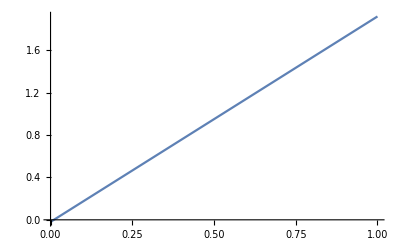

```mathematica
Plot[
-(s1 (m2+s2+m2 s2))/((1+s1) s2)/.{s1->0.02,s2->-0.01},{m2,0,1}
]
```

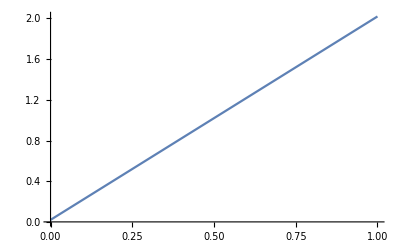

```mathematica
Plot[
-(s1 (m2-s2))/s2/.{s1->0.02,s2->-0.01},{m2,0,1}
]
```

```mathematica
Plot[]
```